```mathematica
distribucionBE[frecuencia_,temp_] := 1/(Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)]-1);
distribucionMB[frecuencia_, temp_]:=1/Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)];
distribucion[frecuencia_,temp_]:=((PlanckConstant*frecuencia)/(BoltzmannConstant*temp))^-1;
distribucion[10000,1]
```

132650.

FindRoot::precw: The precision of the argument function (√(-0.375594+w) (0.250396+w)^2 Cosh[(√(0.375594+w))/2] Sin[(√(-0.375594+w))/2]+(-0.250396+w)^2 √(0.375594+w) Cos[(√(-0.375594+w))/2] Sinh[(√(0.375594+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function (√(-375595.+w) (250396.+w)^2 Cosh[(√(375595.+w))/2] Sin[(√(-375595.+w))/2]+(-250396.+w)^2 √(375595.+w) Cos[(√(-375595.+w))/2] Sinh[(√(375595.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function (√(-1.50088×10^6+w) (1.00058×10^6+w)^2 Cosh[(√(1.50088×10^6+w))/2] Sin[(√(-1.50088×10^6+w))/2]+(-1.00058×10^6+w)^2 √(1.50088×10^6+w) Cos[(√(-1.50088×10^6+w))/2] Sinh[(√(1.50088×10^6+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

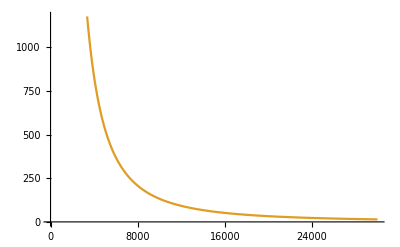

```mathematica
Plot[{distribucion[frecuenciaωSimPositivo[x,1]],distribucionBE[frecuenciaωSimPositivo[x,1],1]},{x,0,30000}]
```